```mathematica
ClearAll["Global`*"]
```

```mathematica
v=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/polygon/solution/vertices.csv"]
v=Table[v[[i]],{i,2,Length[v]}]
```

```mathematica
dummy=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/polygon/solution/edges.csv"]
```

```mathematica
For[t={};i=2,i<=Length[dummy],i++,
If[dummy[[i,3]]==6,
AppendTo[t,{{v[[dummy[[i,1]]]][[2]],v[[dummy[[i,1]]]][[3]]},{v[[dummy[[i,2]]]][[2]],v[[dummy[[i,2]]]][[3]]}}]
]
]
```

```mathematica
t
```

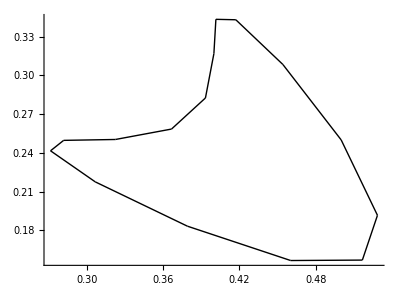

```mathematica
Graphics[Line[t],Axes->True]
```